# NarvAC

### Autor: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

El objetivo de este proyecto es crear una máquina capaz de realizar cómputo a partir de compuertas lógicas.

-Graphics-

## Auxiliar

Ejecución

Definiciones necesarias para imitar el comportamiento de ciertos circuitos. MemoryEvaluate funciona creando un símbolo especial por cada tag, permitiendo así evaluar la función con el argumento de la evaluación anterior. Esto realiza una anidación de la función definida en expr por cada evaluación sucesiva.

```mathematica
HalfSplit[l_]:=Block[{len},
len = Length[l]/2;
{Take[l,len],Drop[l,len]}
];

SetAttributes[MemoryEvaluate,HoldAll];
MemoryEvaluate[expr_,tag_]:=Block[{},
If[Head[SpecialSymbol[tag]]== SpecialSymbol,
SpecialSymbol[tag] = 0;
];
SpecialSymbol[tag] = ReleaseHold[expr[SpecialSymbol[tag]]];
Return[SpecialSymbol[tag]];
];

Unprotect[BitAnd];
BitAnd[1,x_]:=x;
BitAnd[x_,1]:=x;
Protect[BitAnd];

Unprotect[BitNot];
BitNot[0] := 1;
BitNot[1] := 0;
Protect[BitAnd];
```

### Ejemplo

Ejemplo de uso de MemoryEvaluate

```mathematica
MemoryEvaluate[f,"Example"]
```

```mathematica
MemoryEvaluate[f,"Example"]
```

```mathematica
MemoryEvaluate[f,"Example"]
```

Visualización

### Visualización de resultados de circuitos.

```mathematica
VisualizeAdder[module_,inputSize_,flagName_] := Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,Apply[module,#]]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{flagName,"Result"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];

VisualizeMultiplexer[mux_,inputSize_]:=Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,{mux[#,Take[Alphabet[],2^inputSize]]}]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{"Selection"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];
```

### Visualización de la estructura de árbol

#### Evaluar sólo el encabezado

```mathematica
EvalWithValues[expr_,values_]:=expr/.values;
EvaluateHead[expr_,values_]:=ReplaceRepeated[expr,{f_Symbol[arg__]:>EvalWithValues[f[arg],values][arg]}];
```

```mathematica
DenestEvaluating[expr_,values_]:=
ReplaceAll[
Map[
If[Head[#]=== List,
DenestEvaluating[#,values],
EvaluateHead[#,values]
]&,
Level[expr,1]
],
values
];
```

#### Ejemplos (solo relevantes para la visualización)

```mathematica
expr = ALUAdder[{a1,a2},{b1,b2}]
```

```mathematica
DenestEvaluating[expr,{a1->0,a2->1,b1->0,b2->1}]
```

#### Graficar expresión

```mathematica
SetOptions[$FrontEndSession,AutoStyleOptions->{"HighlightFormattingErrors"->False}];

SelectColor[coord_,edge_]:=
If[Head[First[edge]] =!=Symbol,
If[Last[edge]==1,
{ColorData["HTML"]["LawnGreen"],Line[coord]},
{GrayLevel[0.3],Line[coord]}
]
,
If[Head[Last[edge]] =!=Symbol,
If[Last[edge]==1,
{ColorData["HTML"]["LawnGreen"],Line[coord]},
{GrayLevel[0.3],Line[coord]}
]
,
{ColorData["HTML"]["SteelBlue"],Line[coord]}
]
];

PlotExpression[expr_,values_]:=Rasterize[
TreeForm[DenestEvaluating[expr,values],
VertexRenderingFunction->None,
EdgeRenderingFunction->(
ReleaseHold[SelectColor[#,#2]]&),
AspectRatio->1,
Background->Black
]
]
```

Forma alternativa, evaluar para cambiar de estilo

```mathematica
rules = Thread[{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association}->RandomColor[8]]
```

```mathematica
rules = {List->RGBColor[0.9623193882679648, 0.03514590058516487, 0.5539986197144429],BitOr->RGBColor[0.4321980817159774, 0.2972881311143414, 0.8969615660840642],BitAnd->RGBColor[0.6169280698743795, 0.1544371325597096, 0.8820569584091065],BitXor->RGBColor[0.9874612892962218, 0.48338687273679914, 0.005451085259005284],BitNot->RGBColor[0.7522328767507627, 0.02288629260249042, 0.6068775359049052],0->RGBColor[0.8168930920991375, 0.6831040880488453, 0.015427844326858287],1->RGBColor[0.48095945766677284, 0.13406415167597507, 0.13390101182675873],Association->RGBColor[0.2947209985997292, 0.6655069057711502, 0.8296298604565884]};
GetColorForPlotExpression[f_,rules_]:=ReplaceAll[f,rules];
PlotExpression[expr_,values_]:=Block[{plt1,plt2,symbols,symbolRules},
plt1 = TreeForm[
DenestEvaluating[expr,values],
VertexRenderingFunction->None,
EdgeRenderingFunction->(
ReleaseHold[SelectColor[#,#2]]&),
AspectRatio->0.4,
Background->Black,
ImageSize->2200
];

symbols = GetSymbols[expr];
symbolRules = Join[rules,Thread[symbols->White]];
plt2 = TreeForm[
expr,
VertexRenderingFunction->({ReleaseHold[GetColorForPlotExpression[#2,symbolRules]],Disk[#,.05]}&),
EdgeRenderingFunction->None,
AspectRatio->0.4,
Background->Black,
ImageSize->2200
];

ImageAdd[Rasterize[plt1],0.4*Rasterize[plt2]]
];
```

#### Graficar sistema (sin necesidad de especificar el valor de las variables)

```mathematica
GetSymbols[system_]:=Complement[
DeleteDuplicates[Level[system,{-1},Heads->True]],
{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association}
];

SetOptions[$FrontEndSession,DynamicEvaluationTimeout->20];
PlotInteractiveSystem[system_,plotVertex_:Automatic]:=DynamicModule[{symbols,controllerSymbols,boxes,controls,plot},
Clear["*Ctrl"];
symbols = GetSymbols[system];
controllerSymbols = Map[Symbol[StringJoin[SymbolName[#],"Ctrl"]]&,symbols];
boxes = Map[Checkbox[Dynamic[#],{0,1}]&,controllerSymbols];

controls = Panel[Multicolumn[Map[Row[{SymbolName[#[[1]]]<>": ",#[[2]]}]&,Transpose[{symbols,boxes}]],5],Style["Control",Bold]];

plot = Dynamic[
TreeForm[
DenestEvaluating[system,Thread[symbols->controllerSymbols]],
EdgeRenderingFunction->(
ReleaseHold[SelectColor[#,#2]]&),
VertexRenderingFunction->plotVertex,
ImageSize->400,
AspectRatio->1/2,
Background->Black
]
];

Column[{controls,Framed[plot]}]
];
```

## ALU

Half adder

El Half Adder, Full Adder, y Ripple Carry Adder son circuitos para implementar sumas

-Graphics-

```mathematica
HalfAdder[a_,b_]:={BitAnd[a,b],BitXor[a,b]};
```

### Ejemplo

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

### Visualización

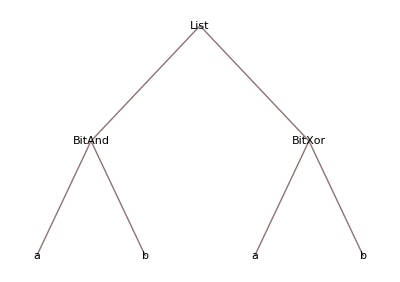

```mathematica
TreeForm[HalfAdder[a,b]]
```

```mathematica
HalfAdder[a,b]
```

{BitAnd[a,b],BitXor[a,b]}

Full adder

-Graphics-

```mathematica
FullAdder[a_,b_,c_]:=Block[{halfAdd1,halfAdd2},
halfAdd1 = HalfAdder[a,b];
halfAdd2 = HalfAdder[Last[halfAdd1],c];
{BitOr[First[halfAdd1],First[halfAdd2]],Last[halfAdd2]}
];
```

### Ejemplo

```mathematica
VisualizeAdder[FullAdder,3,"Carry"]
```

A | B | C | Carry | Result
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1

### Visualización

```mathematica
TreeForm[FullAdder[a,b,c]]
```

Ripple carry adder

-Graphics-

```mathematica
ALUAdder[A_,B_,carry_:0]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[B];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{carry,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{First[bigEndianSum],Rest[bigEndianSum]}];
];
```

### Ejemplo

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUAdder,Transpose[pairs]];
labels = {"A","B","Carry","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Carry | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 0 | {0,1}
{0,0} | {1,0} | 0 | {1,0}
{0,0} | {1,1} | 0 | {1,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {1,0}
{0,1} | {1,0} | 0 | {1,1}
{0,1} | {1,1} | 1 | {0,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {1,1}
{1,0} | {1,0} | 1 | {0,0}
{1,0} | {1,1} | 1 | {0,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 1 | {0,0}
{1,1} | {1,0} | 1 | {0,1}
{1,1} | {1,1} | 1 | {1,0}

### Visualización

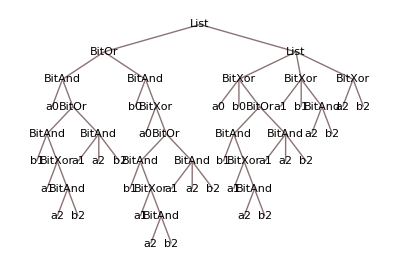

```mathematica
TreeForm[ALUAdder[{a0,a1,a2},{b0,b1,b2}]]
```

En esencia no deja de ser una composición de operaciones binarias

```mathematica
ALUAdder[{a0,a1,a2},{b0,b1,b2}]
```

{BitOr[BitAnd[a0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]],BitAnd[b0,BitXor[a0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]]]],{BitXor[a0,b0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]],BitXor[a1,b1,BitAnd[a2,b2]],BitXor[a2,b2]}}

Substractor

```mathematica
ALUSubstractor[A_,B_,borrow_:1]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[BitNot[B]];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{borrow,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{BitNot[First[bigEndianSum]],Rest[bigEndianSum]}];
];
```

### Ejemplo

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUSubstractor,Transpose[pairs]];
labels = {"A","B","Borrow","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Borrow | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 1 | {1,1}
{0,0} | {1,0} | 1 | {1,0}
{0,0} | {1,1} | 1 | {0,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {0,0}
{0,1} | {1,0} | 1 | {1,1}
{0,1} | {1,1} | 1 | {1,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {0,1}
{1,0} | {1,0} | 0 | {0,0}
{1,0} | {1,1} | 1 | {1,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 0 | {1,0}
{1,1} | {1,0} | 0 | {0,1}
{1,1} | {1,1} | 0 | {0,0}

### Visualización

```mathematica
TreeForm[ALUSubstractor[{a0,a1,a2},{b0,b1,b2}]]
```

Opcodes

```mathematica
aluMnemonics = {"Add","Substract","Increment","Decrement","Pass"};
aluOpcodes = Thread[aluMnemonics->Take[Tuples[{0,1},3],Length[aluMnemonics]]];
revAluOpcodes = Map[Reverse,aluOpcodes];
ALUOpCode[mnemonic_]:=ReplaceAll[mnemonic,aluOpcodes];
```

```mathematica
Column@aluOpcodes
```

Add→{0,0,0}
Substract→{0,0,1}
Increment→{0,1,0}
Decrement→{0,1,1}
Pass→{1,0,0}

Ejecución

Banderas

```mathematica
ALUZero[a_]:=BitNot[Apply[BitOr,a]];
ALUNotZero[a_]:=Apply[BitOr,a];
ALUParity[a_]:=Apply[BitXor,a];
```

Ejecución

```mathematica
ALUExecute[opcode_,a_,b_]:=Block[
{
add,substract,
increment,decrement,pass,output,positiveFlag,
negativeFlag,parityFlag
},

add = ALUAdder[a,b];
substract = ALUSubstractor[a,b];
increment = ALUAdder[PadLeft[{1},Length[a]],a];
decrement = ALUSubstractor[a,PadLeft[{1},Length[a]]];
pass = a;

output = Mux8to1[opcode,
MuxInputByOpcode[3,
{
{ALUOpCode["Add"],Last[add]},
{ALUOpCode["Substract"],Last[substract]},
{ALUOpCode["Increment"],Last[increment]},
{ALUOpCode["Decrement"],Last[decrement]},
{ALUOpCode["Pass"],pass}
}
]
];

positiveFlag = Mux8to1[opcode,
MuxInputByOpcode[3,
{
{ALUOpCode["Add"],1},
{ALUOpCode["Substract"],BitNot[First[substract]]},
{ALUOpCode["Increment"],1},
{ALUOpCode["Decrement"],BitNot[First[decrement]]},
{ALUOpCode["Pass"],0}
}
]
];

negativeFlag = Mux8to1[opcode,
MuxInputByOpcode[3,
{
{ALUOpCode["Add"],0},
{ALUOpCode["Substract"],First[substract]},
{ALUOpCode["Increment"],0},
{ALUOpCode["Decrement"],First[decrement]},
{ALUOpCode["Pass"],0}
}
]
];

Return[{<|"Positive"->positiveFlag,"Negative"->negativeFlag,"Zero"->ALUZero[output],"NotZero"->ALUNotZero[output],"Parity"->ALUParity[output]|>,output}];
];

ALUClear[]:=Block[{},
WriteFlag[0,"ALUFlagPositive"];
WriteFlag[0,"ALUFlagNegative"];
WriteFlag[0,"ALUFlagZero"];
WriteFlag[0,"ALUFlagNotZero"];
WriteFlag[0,"ALUFlagParity"];
];
```

### Visualización

Complejidad de una ALU de 2 bits

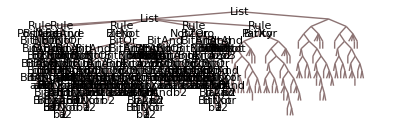

```mathematica
TreeForm[Normal[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],PlotRangePadding->Scaled[.002]]
```

Complejidad de una ALU de 8 bits

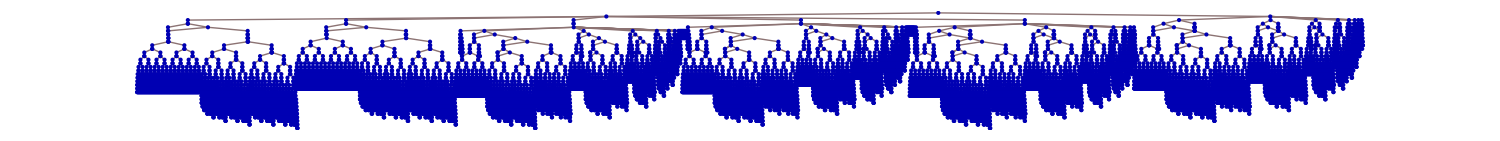

```mathematica
TreeForm[Normal[ALUExecute[{o1,o2,o3},{a1,a2,a3,a4,a5,a6,a7,a8},{b1,b2,b3,b4,b5,b6,b7,b8}]],VertexLabeling->Automatic,ImageSize->1500]
```

## Multiplexor

2 a 1

-Graphics-

```mathematica
Mux2to1[{select_},{input1_,input2_}]:=BitOr[BitAnd[input1,BitNot[select]],BitAnd[input2,select]];
```

4 a 1

-Graphics-

```mathematica
Mux4to1[{select1_,select2_},{input1_,input2_,input3_,input4_}]:=Mux2to1[
{select1},
{
Mux2to1[{select2},{input1,input2}],
Mux2to1[{select2},{input3,input4}]
}
];
```

8 a 1

-Graphics-

```mathematica
Mux8to1[{select1_,select2_,select3_},{input1_,input2_,input3_,input4_,input5_,input6_,input7_,input8_}]:=
Mux2to1[
{select1},
{
Mux4to1[{select2,select3},{input1,input2,input3,input4}],
Mux4to1[{select2,select3},{input5,input6,input7,input8}]
}
];
```

Visualizaciones

Resultado

```mathematica
{VisualizeMultiplexer[Mux2to1,1],VisualizeMultiplexer[Mux4to1,2],VisualizeMultiplexer[Mux8to1,3]}
```

Árbol de complejidad

```mathematica
TreeForm[Mux8to1[{s1,s2,s3},{i1,i2,i3,i4,i5,i6,i7,i8}]]
```

Grid cuadrado

```mathematica
MultiplexerNTo1[2,{select_},input__]:=BitOr[BitAnd[First[input],BitNot[select]],BitAnd[Last[input],select]];
MultiplexerNTo1[n_,select_,input__]:=Block[{partInput},
partInput = HalfSplit[input];
MultiplexerNTo1[
2,
{First[select]},
{
MultiplexerNTo1[n/2,Rest[select],First[partInput]],
MultiplexerNTo1[n/2,Rest[select],Last[partInput]]
}
]
];
```

### Ejemplo

```mathematica
VisualizeMultiplexer[MultiplexerNTo1[16,#1,#2]&,4]
```

A | B | C | D | Selection
0 | 0 | 0 | 0 | a
0 | 0 | 0 | 1 | b
0 | 0 | 1 | 0 | c
0 | 0 | 1 | 1 | d
0 | 1 | 0 | 0 | e
0 | 1 | 0 | 1 | f
0 | 1 | 1 | 0 | g
0 | 1 | 1 | 1 | h
1 | 0 | 0 | 0 | i
1 | 0 | 0 | 1 | j
1 | 0 | 1 | 0 | k
1 | 0 | 1 | 1 | l
1 | 1 | 0 | 0 | m
1 | 1 | 0 | 1 | n
1 | 1 | 1 | 0 | o
1 | 1 | 1 | 1 | p

### Visualización

```mathematica
selectSymbols = Table[Symbol["s"<>ToString[i]],{i,1,8}];
inputSymbols = Table[Symbol["i"<>ToString[i]],{i,1,256}];
TreeForm[MultiplexerNTo1[256,selectSymbols,inputSymbols],VertexLabeling->Automatic,ImageSize->1300]
```

## Selección de Opcode por Multiplexor

Función auxiliar para ordenar los pares entrada-salida en los multiplexores

```mathematica
MuxInputByOpcode[n_,opcodeAndOutput_]:=Block[{addresses,missing},
addresses = Tuples[{0,1},n]; (* Generate the list of all opcode inputs.  *)
missing = Thread[{Complement[addresses,opcodeAndOutput[[All,1]]],0}]; (* Select the ones with no inputs and map them to zero. *)
Return[SortBy[Join[missing,opcodeAndOutput],First][[All,2]]] (* Join missing opcodes with the given opcodes and sort. *)
];
```

### Ejemplo

```mathematica
MuxInputByOpcode[3,
{
{ALUOpCode["Add"],add},
{ALUOpCode["Substract"],substract},
{ALUOpCode["Decrement"],decrement}
}
]
```

{add,substract,0,decrement,0,0,0,0}

## Memoria

And-Or Latch

De la Wikipedia: In electronics, a flip-flop or latch is a circuit that has two stable states and can be used to store state information. A flip-flop is a bistable multivibrator. The circuit can be made to change state by signals applied to one or more control inputs and will have one or two outputs. It is the basic storage element in sequential logic. Flip-flops and latches are fundamental building blocks of digital electronics systems used in computers, communications, and many other types of systems.

-Graphics-

```mathematica
AndOrLatch[set_,reset_,tag_]:=MemoryEvaluate[BitAnd[BitOr[#,set],BitNot[reset]]&,tag];
```

Este es el circuito base para todos los tipos de memoria que se utiliza a continuación

### Visualización

```mathematica
Table[TreeForm[AndOrLatch[set,reset,tag],ImageSize->Medium],3]
```

Gated Latch

-Graphics-

Fuente: Crash Course Computer Science

```mathematica
GatedLatch[dataInput_,writeEnable_,tag_]:=AndOrLatch[BitAnd[dataInput,writeEnable],BitAnd[BitNot[dataInput],writeEnable],tag];
```

Estos circuitos nos sirven para guardar banderas de 1 bit

```mathematica
ReadFlag[tag_]:=GatedLatch[0,0,tag];
WriteFlag[dataInput_,tag_]:=GatedLatch[dataInput,1,tag];
```

### Visualización

```mathematica
Table[TreeForm[GatedLatch[dataInput,writeEnable,tag],ImageSize->Medium,VertexRenderingFunction->None],3]
```

Celda

Fuente: Crash Course Computer Science

```mathematica
Bit8AddressCell[dataInput_,writeEnable_,address__,tag_]:=
GatedLatch[
dataInput,
writeEnable,
StringJoin[
tag,
"bit_",
ToString[
MultiplexerNTo1[
256,
address,
Range[256]
]
]
]
];
```

Bloque

Fuente: Crash Course Computer Science

```mathematica
Bit8AddressBlock[dataInput__/;Length[dataInput]==8,writeEnable_,address__,tag_]:=Table[Bit8AddressCell[Part[dataInput,i],writeEnable,address,StringJoin[tag,"bit_",ToString[i]]],{i,8}];

ReadBit8AddressBlock[address__,tag_]:=Bit8AddressBlock[{0,0,0,0,0,0,0,0},0,address,tag];
WriteBit8AddressBlock[dataInput__/;Length[dataInput]==8,address__,tag_]:=Bit8AddressBlock[dataInput,1,address,tag];
```

### Visualización

```mathematica
TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"exampletag"]]
```

```mathematica
TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"exampletag"]]
```

Visualización recursiva interactiva

```mathematica
trees = Table[TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"manip"],VertexLabeling->Automatic,ImageSize->1300],15];
Manipulate[trees[[i]],{i,1,Length[trees],1},SaveDefinitions->True]
```

## Registros

Fuente: Crash Course Computer Science

```mathematica
Bit8Register[dataInput__,writeEnable_,tag_]:=Table[
GatedLatch[
Part[dataInput,index],
writeEnable,
StringJoin[tag,"_bit8register",ToString[index]]
],
{index,1,8}
];
ReadBit8Register[tag_]:=Bit8Register[{0,0,0,0,0,0,0,0},0,tag];
WriteBit8Register[dataInput__,tag_]:=Bit8Register[dataInput,1,tag];
```

## Unidad de control

Auxiliar

Reseteo de la unidad de control

```mathematica
CUClear[]:=Block[{},
WriteBit8Register[{0,0,0,0,0,0,0,0},"AddressRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"InstructionRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"ParameterRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"StackPointerRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"RegisterA"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"RegisterB"];
WriteFlag[0,"Ram Read-Enable"];
WriteFlag[0,"Ram Write-Enable"];
WriteFlag[0,"RegisterA Read-Enable"];
WriteFlag[0,"RegisterB Read-Enable"];
WriteFlag[0,"RegisterA Write-Enable"];
WriteFlag[0,"RegisterB Write-Enable"];
WriteFlag[0,"ALU Opcode"];
WriteFlag[0,"Halt"];
];
```

Opcodes

```mathematica
cpuMnemonics = {
"LoadA","LoadB","SetA","SetB","Store","Add",
"Substract","Increment","Decrement","Jump","JumpPos","JumpNeg","JumpZero","JumpNotZero","JumpOdd",
"Call","Return","Print","Halt"
};
opcodes = Thread[cpuMnemonics->Take[Tuples[{0,1},8],Length[cpuMnemonics]]];
revOpcodes = Map[Reverse,opcodes];
OpCode[mnemonic_]:=ReplaceAll[mnemonic,opcodes];
```

Fetch

```mathematica
CUFetch[]:=Block[{instructionAddress,instruction},
instructionAddress = ReadBit8Register["InstructionAddress"];
instruction = ReadBit8AddressBlock[instructionAddress,"MainMemory"];
WriteBit8Register[instruction,"InstructionRegister"];
];
```

### Visualización

```mathematica
op = WriteBit8Register[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,ReadBit8Register["InstructionAddress"],"MainMemory"],"InstructionRegister"];
```

```mathematica
TreeForm[op]
```

Decode

En decode se escriben las banderas adecuadas que permitirán el paso del resultado a los registros o sectores de memoria adecuados

```mathematica
CUDecode[]:=Block[
{
opcode,ramReadEnable,ramWriteEnable,registerAReadEnable,
registerBReadEnable,registerAWriteEnable,registerBWriteEnable,
aluOpcode,aluInstruction,halt, jumpEnable, jumpNegEnable,
jumpZeroEnable,printEnable,
return = {}
},

opcode = First[HalfSplit[ReadBit8Register["InstructionRegister"]]];
ramReadEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeLoadA[],1},
{OpcodeLoadB[],1}
}
]
];
AppendTo[return,WriteFlag[ramReadEnable,"Ram Read-Enable"]];

ramWriteEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeStoreA[],1}
}
]
];
AppendTo[return,WriteFlag[ramWriteEnable,"Ram Write-Enable"]];


registerAReadEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeStoreA[],1}
}
]
];
AppendTo[return,WriteFlag[registerAReadEnable,"RegisterA Read-Enable"]];


registerBReadEnable =MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeStoreB[],1}
}
]
];
AppendTo[return,WriteFlag[registerBReadEnable,"RegisterB Read-Enable"]];

registerAWriteEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeLoadA[],1},
{OpcodeAdd[],1},
{OpcodeSubstract[],1},
{OpcodeIncrement[],1}
}
]
];
AppendTo[return,WriteFlag[registerAWriteEnable,"RegisterA Write-Enable"]];

registerBWriteEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeLoadB[],1}
}
]
];
AppendTo[return,WriteFlag[registerBWriteEnable,"RegisterB Write-Enable"]];

jumpEnable = MultiplexerNTo1[16,opcode,
MuxInputByOpcode[8,
{
{OpcodeJump[],1}
}
]
];
AppendTo[return,WriteFlag[jumpEnable,"Jump"]];

jumpNegEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeJumpNeg[],1}
}
]
];
AppendTo[return,WriteFlag[jumpNegEnable,"JumpNeg"]];

jumpZeroEnable = MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeJumpZero[],1}
}
]
];
AppendTo[return,WriteFlag[jumpZeroEnable,"JumpZero"]];

aluInstruction =  MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeAdd[],1},
{OpcodeSubstract[],1},
{OpcodeIncrement[],1}
}
]
];
AppendTo[return,WriteFlag[aluInstruction,"ALU Instruction"]];

aluOpcode =  MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeAdd[],ALUOpcodeAdd[]},
{OpcodeSubstract[],ALUOpcodeSubstract[]},
{OpcodeIncrement[],ALUOpcodeIncrement[]}
}
]
];
AppendTo[return,WriteBit3Register[aluOpcode,"ALU Opcode"]];

printEnable =  MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodePrint[],1}
}
]
];
AppendTo[return,WriteFlag[printEnable,"Print Enable"]];

halt =  MultiplexerNTo1[256,opcode,
MuxInputByOpcode[8,
{
{OpcodeHalt[],1}
}
]
];
AppendTo[return,WriteFlag[halt,"Halt"]];
Return[return];
];
```

### Visualización

```mathematica
op1 = WriteBit8Register[Bit4AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4},"MainMemory"],"InstructionRegister"];
op2 = CUDecode[];
```

```mathematica
TreeForm[op2,VertexLabeling->Automatic]
```

Execute

```mathematica
CUExecute[]:=Block[{param,readFromRam,aluResult,nextInstructionAddress, return = {}},
param = Last[HalfSplit[ReadBit8Register["InstructionRegister"]]];
readFromRam = ReadBit4AddressBlock[param,"MainMemory"];

(* Read operations *)
AppendTo[return,Bit8Register[readFromRam,BitAnd[ReadFlag["RegisterA Write-Enable"],BitNot[ReadFlag["ALU Instruction"]]],"RegisterA"]];
AppendTo[return,Bit8Register[readFromRam,BitAnd[ReadFlag["RegisterB Write-Enable"],BitNot[ReadFlag["ALU Instruction"]]],"RegisterB"]];

(* ALU operations *)
aluResult = ALUExecute[ReadBit3Register["ALU Opcode"],ReadBit8Register["RegisterA"],ReadBit8Register["RegisterB"]];
AppendTo[return,Bit8Register[Last[aluResult],BitAnd[ReadFlag["RegisterA Write-Enable"],ReadFlag["ALU Instruction"]],"RegisterA"]];
AppendTo[return,GatedLatch[First[aluResult]["Overflow"],ReadFlag["ALU Instruction"],"ALUFlagOverflow"]];
AppendTo[return,GatedLatch[First[aluResult]["Negative"],ReadFlag["ALU Instruction"],"ALUFlagNegative"]];
AppendTo[return,GatedLatch[First[aluResult]["Zero"],ReadFlag["ALU Instruction"],"ALUFlagZero"]];
AppendTo[return,GatedLatch[First[aluResult]["Parity"],ReadFlag["ALU Instruction"],"ALUFlagParity"]];

(* Write operations *)
AppendTo[return,Bit4AddressBlock[PadLeft[ReadBit8Register["RegisterA"],8],ReadFlag["Ram Write-Enable"],param,"MainMemory"]];

(* Instruction address operations *)
AppendTo[return,Bit4Register[param,ReadFlag["Jump"],"InstructionAddress"]];
AppendTo[return,Bit4Register[param,BitAnd[ReadFlag["JumpNeg"],ReadFlag["ALUFlagNegative"]],"InstructionAddress"]];

nextInstructionAddress = Last[ALUAdder[ReadBit4Register["InstructionAddress"],{0,0,0,1}]];
AppendTo[return,Bit4Register[nextInstructionAddress,BitAnd[BitNot[ReadFlag["Jump"]],BitNot[ReadFlag["JumpNeg"]]],"InstructionAddress"]];
AppendTo[return,Bit4Register[nextInstructionAddress,BitAnd[ReadFlag["JumpNeg"],BitNot[ReadFlag["ALUFlagNegative"]]],"InstructionAddress"]];

If[ReadFlag["JumpNeg"],Print[ReadBit8Register["RegisterA"]]];

Return[return];
];
```

### Visualización

```mathematica
op1 = CUFetch[];
op2 = CUDecode[];
op3 = CUExecute[];
```

```mathematica
Rasterize[TreeForm[op3,VertexRenderingFunction->None,AspectRatio->1,ImageSize->600]]
```

```mathematica
PlotInteractiveSystem[op3,None]
```

## CPU

Atajos de ejecución

```mathematica
CPUCycle[]:=Block[{},
CUFetch[];
CUDecode[];

If[ReadFlag["Halt"] ≠ 1,CUExecute[]];
];
Execute[program_]:=Block[{steps},
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

steps = Reap[
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];

While[ReadFlag["Halt"] ≠ 1,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];
]
][[2,1]];
Return[steps];
];

Execute[program_,cycles_]:=Block[{steps,iter = 0},
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

steps = Reap[
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];

While[ReadFlag["Halt"] ≠ 1 && iter < cycles,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];
iter++;
]
][[2,1]];
Return[steps];
];
```

## Utilidades

Carga de programa a la memoria

```mathematica
LoadProgram[program_]:=Block[{addresses},
addresses = Map[PadLeft[IntegerDigits[#,2],4]&,Range[0,15]];
MapThread[WriteBit4AddressBlock[#2,#1,"MainMemory"]&,{addresses,program}];
];
ClearProgram[]:=Block[{addresses},
addresses = Map[PadLeft[IntegerDigits[#,2],4]&,Range[0,15]];
Map[WriteBit4AddressBlock[{0,0,0,0,0,0,0,0},#1,"MainMemory"]&,addresses];
];
```

Compilar desde ensamblador

```mathematica
assemblyOpcodes = Map[Reverse,cpuMnemonics];
HexToBinary[n_,pad_:4]:=PadLeft[IntegerDigits[FromDigits[n,16],2],pad];
DecToBinary[n_,pad_:4]:=PadLeft[IntegerDigits[FromDigits[n,10],2],pad];
BinaryToHex[n_]:=BaseForm[FromDigits[n,2],16];
FromInstructionToBitcode[instruction_]:= Switch[Length[Rest[instruction]],
0,Join[First[instruction],{0,0,0,0}],
1,Join[First[instruction],DecToBinary[Last[instruction]]],
2,Join[First[instruction],DecToBinary[Part[instruction,2],2],DecToBinary[Part[instruction,3],2]]
];
FromInstructionTableToBitcode[code_]:=Map[FromInstructionToBitcode,ReplaceAll[Map[StringSplit,StringSplit[code,"\n"]], assemblyOpcodes]];
AssemblyCompile[code_]:=PadRight[FromInstructionTableToBitcode[code],16,{{0,0,0,0,0,0,0,0}}];
```

Gráficas

```mathematica
PlotRAM[]:=Block[{addresses,ram,currentAddress},
addresses = Map[PadLeft[IntegerDigits[#,2],4]&,Range[0,15]];
ram = Map[ReadBit4AddressBlock[#,"MainMemory"]&,addresses];
currentAddress = FromDigits[ReadBit4Register["InstructionAddress"],2];
Panel[Grid[Join[{{"Address","Value"}},Thread[{Range[0,15],ram}]],Background->{None,{1->LightGreen,(currentAddress+2)->Yellow}},Frame->All],Style["RAM",Bold]]
];
ALUStatusPlot[]:=Panel[
Grid[{
{"Overflow: ",ReadFlag["ALUFlagOverflow"]},
{"Negative: ",ReadFlag["ALUFlagNegative"]},
{"Zero: ",ReadFlag["ALUFlagZero"]},
{"Parity: ",ReadFlag["ALUFlagParity"]}
},
Frame->All,
Background->{{LightRed},None}
],
Style["ALU Status",Bold]
];

CUStatusPlot[]:=Block[{mainRegisters,instructionRegisters,flagsStatus},
mainRegisters = Grid[
{
{"Register A","Register B"},
{Row[ReadBit8Register["RegisterA"]],Row[ReadBit8Register["RegisterB"]]}
},
Frame->All,
Background->{None,{LightGreen}}
];

instructionRegisters = Grid[
{
{"Instruction Register","Address Register"},
{
Grid[
{
{"Opcode","Parameter"},
Map[Row,HalfSplit[ReadBit8Register["InstructionRegister"]]],
{First[HalfSplit[ReadBit8Register["InstructionRegister"]]]/.cpuMnemonics,BinaryToHex[Last[HalfSplit[ReadBit8Register["InstructionRegister"]]]]}
},
Frame->All,Background->{None,{LightCyan}}
],
Row[ReadBit4Register["InstructionAddress"]]
}
},
Frame->All,
Background->{None,{LightBlue}}
];

flagsStatus = Grid[{
{"Ram Read-Enable: ",ReadFlag["Ram Read-Enable"]},
{"Ram Write-Enable: ",ReadFlag["Ram Write-Enable"]},
{"RegisterA Read-Enable: ",ReadFlag["RegisterA Read-Enable"]},
{"RegisterB Read-Enable: ",ReadFlag["RegisterB Read-Enable"]},
{"RegisterA Write-Enable: ",ReadFlag["RegisterA Write-Enable"]},
{"RegisterB Write-Enable: ",ReadFlag["RegisterB Write-Enable"]},
{"Jump: ",ReadFlag["Jump"]},
{"JumpNeg: ",ReadFlag["JumpNeg"]},
{"JumpZero: ",ReadFlag["JumpZero"]},
{"ALU Instruction: ",ReadFlag["ALU Instruction"]},
{"ALU Opcode: ",ReadBit3Register["ALU Opcode"]/.aluMnemonics},
{"Halt: ",ReadFlag["Halt"]}
},
Frame->All,
Background->{{LightRed},None}
];

Panel[Column[{mainRegisters,instructionRegisters,flagsStatus}],Style["CU Status",Bold],ImageSize->250]
];

CPUPlot[]:=Panel[Grid[{{ALUStatusPlot[],CUStatusPlot[],PlotRAM[],CPUModelPlot[model]}},Alignment->Top],Style["CPU",Bold]];
ExecutionPlot[program_]:=DynamicModule[{result = Execute[program]},
Manipulate[Part[result,i],{i,1,Length[result],1}]
];
ExecutionPlot[program_,cycles_]:=DynamicModule[{result = Execute[program,cycles]},
Manipulate[Part[result,i],{i,1,Length[result],1}]
];

CreateCPUModel[]:=Block[{cpuStep1,cpuStep2,cpuStep3,b1,b2,b3,b4,b5,b6,b7,b8},
ClearProgram[];
ALUClear[];
CUClear[];
cpuStep1 = WriteBit8Register[{b1,b2,b3,b4,b5,b6,b7,b8},"InstructionRegister"];
cpuStep2 = CUDecode[];
cpuStep3 = CUExecute[];
Return[cpuStep3];
];
model = CreateCPUModel[];

CPUModelPlot[model_]:=Block[{argument,b1,b2,b3,b4,b5,b6,b7,b8},
argument = Thread[{b1,b2,b3,b4,b5,b6,b7,b8}->ReadBit4AddressBlock[ReadBit4Register["InstructionAddress"],"MainMemory"]];
Panel[PlotExpression[model,argument],Style["Model plot",Bold]]
];
```

## Ejecución

```mathematica
code = "
LoadA 14
LoadB 15
Substract 1 0
JumpNeg 5
Jump 2
Add 1 0
StoreA 13
Halt
";

program = AssemblyCompile[code];
setValues = {{15,DecToBinary["110",8]},{16,DecToBinary["5",8]}};
MapThread[(Part[program,#1]=#2)&,Transpose[setValues]];
```

```mathematica
ExecutionPlot[program,2]
```

### Visualización de ejecución de modelo del sistema

```mathematica
CPUModelPlotToExport[model_]:=Block[{argument,b1,b2,b3,b4,b5,b6,b7,b8},
argument = Thread[{b1,b2,b3,b4,b5,b6,b7,b8}->ReadBit4AddressBlock[ReadBit4Register["InstructionAddress"],"MainMemory"]];
PlotExpression[model,argument]
];

ExecuteModel[program_]:=Block[{steps},
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

steps = Reap[
CUFetch[];
CUDecode[];
Sow[CPUModelPlotToExport[Last[model]]];

While[ReadFlag["Halt"] ≠ 1,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[CPUModelPlotToExport[Last[model]]];
]
][[2,1]];
Return[steps];
];
```

```mathematica
code = "
LoadA 14
LoadB 15
Substract 1 0
JumpNeg 10
StoreA 12
LoadA 13
Increment
StoreA 13
LoadA 12
Jump 2
Halt
";
program = AssemblyCompile[code];
setValues = {{13+1,DecToBinary["0",8]},{14+1,DecToBinary["110",8]},{15+1,DecToBinary["5",8]}};
MapThread[(Part[program,#1]=#2)&,Transpose[setValues]];
```

```mathematica
imgs = ExecuteModel[program];
```

```mathematica
exportPath = FileNameJoin[{NotebookDirectory[],"plots","image"}];
Table[Export[StringJoin[exportPath,IntegerString[i,10,4],".png"],imgs[[i]]],{i,1,Length[imgs]}];
```